# Contact rates

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Dropbox/current-projects/global-migration/age-structure/scripts

```mathematica
SetDirectory[".."]
```

/Users/trvrb/Dropbox/current-projects/global-migration/age-structure

```mathematica
types={"h3","h1","vic","yam"};
```

### Type colors

```mathematica
yC=RGBColor[0.893,0.385,0.248];
```

```mathematica
vC=RGBColor[0.894,0.664,0.303];
```

```mathematica
h1C=RGBColor[0.323,0.34,0.805];
```

```mathematica
h3C=RGBColor[0.374,0.625,0.766];
```

```mathematica
typeColors={h3C,h1C,vC,yC};
```

```mathematica
typeColorRules=MapThread[#1->#2&,{{"H3N2","H1N1","Vic","Yam"},typeColors}];
```

```mathematica
imageResolution=300;
```

## Demographic structure

Children are 15 and under

```mathematica
ukChildrenPro=CountryData["UnitedKingdom","ChildPopulation"]/CountryData["UnitedKingdom","Population"]
```

0.172233

```mathematica
ausChildrenPro=CountryData["Australia","ChildPopulation"]/CountryData["Australia","Population"]
```

0.187894

```mathematica
childrenPro=Mean[{ukChildrenPro,ausChildrenPro}]
```

0.180064

```mathematica
adultPro=1-childrenPro
```

0.819936

## Bins

```mathematica
bins={{0,10},{11,15},{16,19},{20,24},{25,34},{35,44},{45,54},{55,59},{60,64},{65,74},{75,100}};
```

## Air travel

### Full distribution

```mathematica
heathrow=Drop[Import["data/heathrow.tsv","Table"],1];
```

```mathematica
gatwick=Drop[Import["data/gatwick.tsv","Table"],1];
```

```mathematica
travel=Mean[{heathrow,gatwick}][[All,3]];
```

```mathematica
lines=MapThread[{{#1[[1]],#2},{#1[[2]],#2}}&,{bins,travel}];
```

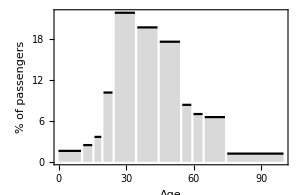

```mathematica
fig=ListLinePlot[lines,ImageSize->300,AspectRatio->0.65,FrameLabel->{"Age","% of passengers"},PlotStyle->Black,FillingStyle->LightGray,Filling->Axis]
```

```mathematica
Export["figures/air-travel-by-age.pdf",fig,"PDF"]
```

figures/air-travel-by-age.pdf

```mathematica
Export["figures/air-travel-by-age.png",fig,"PNG",ImageResolution->imageResolution]
```

figures/air-travel-by-age.png

### Two compartments

```mathematica
threshold=2;
```

```mathematica
Total[travel[[1;;2]]]
```

4.05

```mathematica
Total[travel[[3;;-1]]]
```

96.05

```mathematica
childrenRate=Total[travel[[1;;2]]]/childrenPro
```

22.492

```mathematica
adultRate=Total[travel[[3;;-1]]]/adultPro
```

117.143

```mathematica
childrenRatio=childrenRate/adultRate
```

0.192004

## Incidence

```mathematica
cutoff=6;
```

```mathematica
typeIndex=1;ageIndex=3;
```

```mathematica
inc=Import["data/melb-isolations.tsv","Table"];
```

```mathematica
header=inc[[1]]
```

{virus,strain,age_of_infection}

```mathematica
inc=Drop[inc,1];
```

```mathematica
types={"H3","H1","B"}
```

{H3,H1,B}

```mathematica
inc=Cases[inc,x_/;x[[ageIndex]]≥cutoff&&x[[ageIndex]]≤100];
```

```mathematica
h3Ages=Cases[inc,x_/;x[[typeIndex]]=="H3"][[All,ageIndex]];
```

```mathematica
h1Ages=Cases[inc,x_/;x[[typeIndex]]=="H1"][[All,ageIndex]];
```

```mathematica
bAges=Cases[inc,x_/;x[[typeIndex]]=="B"][[All,ageIndex]];
```

```mathematica
means=Map[Mean,{h3Ages,h1Ages,bAges}]
```

{35.2976,24.9527,24.2426}

```mathematica
Map[Round[Median[#],0.01]&,{h3Ages,h1Ages,bAges}]
```

{30.,20.,16.}

```mathematica
LocationTest[{h3Ages,h1Ages},0,{"TestDataTable",All}]
```

| Statistic | P-Value
Mann-Whitney | 1.07289×10^6 | 4.61442×10^-29

```mathematica
LocationTest[{h3Ages,bAges},0,{"TestDataTable",All}]
```

| Statistic | P-Value
Mann-Whitney | 2.17806×10^6 | 1.23746×10^-62

```mathematica
LocationTest[{h1Ages,bAges},0,{"TestDataTable",All}]
```

| Statistic | P-Value
Mann-Whitney | 496849. | 0.0405655

```mathematica
fig=Grid[Partition[MapThread[Histogram[#1,{0,100,2},AspectRatio->0.65,ImageSize->300,ChartBaseStyle->Directive[EdgeForm[Thin]],ChartStyle->#2,PlotLabel->#3<>" mean age = "<>ToString[Round[#4,0.1]],FrameLabel->{"Age","Count"}]&,{{h3Ages,h1Ages,bAges},{h3C,h1C,vC},{"H3","H1","B"},means}],3],Spacings->{0,0}];
```

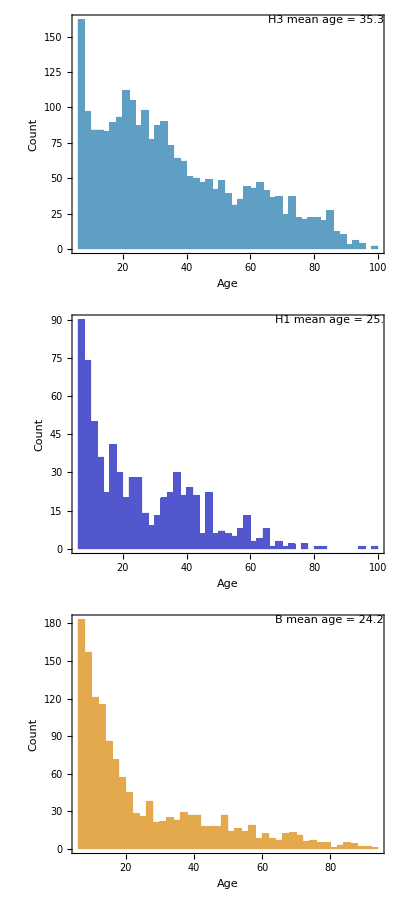

```mathematica
fig=Grid[Partition[MapThread[Histogram[#1,{0,100,2},AspectRatio->0.3,ImageSize->400,ChartBaseStyle->Directive[EdgeForm[Thin]],ChartStyle->#2,Epilog->Style[Text[#3<>" mean age = "<>ToString[Round[#4,0.1]],Scaled[{1,1}],{1,1}],FontFamily->"Helvetica",FontSize->11],FrameLabel->{"Age","Count"}]&,{{h3Ages,h1Ages,bAges},{h3C,h1C,vC},{"H3","H1","B"},means}],1],Spacings->{0,0}]
```

```mathematica
Export["figures/incidence-by-age.pdf",fig,"PDF"]
```

figures/incidence-by-age.pdf

```mathematica
Export["figures/incidence-by-age.png",fig,"PNG",ImageResolution->imageResolution]
```

figures/incidence-by-age.png

```mathematica
h3Inc=With[{counts=N[BinCounts[h3Ages,{Append[bins[[All,1]],100]}]]},counts/Total[counts]];
```

```mathematica
h1Inc=With[{counts=N[BinCounts[h1Ages,{Append[bins[[All,1]],100]}]]},counts/Total[counts]];
```

```mathematica
bInc=With[{counts=N[BinCounts[bAges,{Append[bins[[All,1]],100]}]]},counts/Total[counts]];
```

```mathematica
ListLinePlot[{N[MapThread[{Mean[#1],#2}&,{bins,h3Inc}]],N[MapThread[{Mean[#1],#2}&,{bins,h1Inc}]],N[MapThread[{Mean[#1],#2}&,{bins,bInc}]]},PlotStyle->{h3C,h1C,vC},PlotMarkers->Automatic,ImageSize->300,FrameLabel->{"Age","% of passengers"}];
```

### Contact rates

```mathematica
contactRates=Round[Map[Total[#*travel]&,{h3Inc,h1Inc,bInc}],0.1]
```

{10.8,9.4,7.5}

```mathematica
Round[contactRates/Max[contactRates],0.01]
```

{1.,0.87,0.69}

### Two compartments

```mathematica
h3ChildrenPro=N[Count[h3Ages,x_/;x<19]/Length[h3Ages]]
```

0.264986

```mathematica
h1ChildrenPro=N[Count[h1Ages,x_/;x<19]/Length[h1Ages]]
```

0.471182

```mathematica
bChildrenPro=N[Count[bAges,x_/;x<19]/Length[bAges]]
```

0.565954

## Age structured mixing

### Data

```mathematica
files=FileNames["contacts-*","data/"]
```

{data/contacts-belgium.tsv,data/contacts-britain.tsv,data/contacts-finland.tsv,data/contacts-germany.tsv,data/contacts-italy.tsv,data/contacts-luxembourg.tsv,data/contacts-netherlands.tsv,data/contacts-poland.tsv}

```mathematica
contactMatrix=Mean[Map[Import[#,"Table"]&,files]]
```

{{1.68125,0.6525,0.22,0.14125,0.21,0.42375,0.68625,0.49875,0.5925,0.30375,0.195,0.22875,0.2825,0.17875,0.1225},{1.00375,4.21125,0.68375,0.24875,0.15,0.33375,0.53625,0.715,0.48875,0.27875,0.32,0.22875,0.19625,0.2125,0.15},{0.345,0.78625,5.2275,0.775,0.15125,0.0875,0.29,0.46375,0.61125,0.37375,0.25125,0.14125,0.1625,0.1325,0.295},{0.18875,0.22125,0.9275,5.015,0.8675,0.2625,0.18375,0.20625,0.61875,0.615,0.265,0.18375,0.115,0.095,0.2825},{0.295,0.175,0.20125,0.80625,2.12375,0.94625,0.32625,0.23375,0.3875,0.39375,0.3475,0.2675,0.16375,0.115,0.11},{0.58625,0.375,0.14625,0.26375,0.96125,1.42,0.6425,0.41,0.325,0.39375,0.49,0.405,0.30125,0.15625,0.1875},{0.875,0.6525,0.28375,0.165,0.6,0.8325,1.0475,0.65125,0.44625,0.44125,0.365,0.41125,0.4375,0.23875,0.18875},{0.79375,0.83875,0.565,0.31875,0.3725,0.44,0.90125,1.11375,0.59125,0.44875,0.34875,0.31,0.40125,0.27,0.27375},{0.44375,0.7225,0.7975,0.46625,0.33375,0.34375,0.51375,0.71375,0.9975,0.69625,0.45125,0.34875,0.40125,0.33125,0.3175},{0.285,0.31125,0.48125,0.5725,0.5025,0.33125,0.35,0.3675,0.64625,0.83,0.545,0.37375,0.29625,0.22625,0.355},{0.33625,0.23875,0.22375,0.325,0.4325,0.4125,0.3075,0.28,0.38875,0.5375,0.785,0.60375,0.3525,0.26,0.2625},{0.295,0.22375,0.1325,0.155,0.20375,0.26875,0.26375,0.21375,0.1625,0.2925,0.47625,0.81625,0.52375,0.34875,0.24},{0.28125,0.235,0.11875,0.05625,0.08625,0.16125,0.19875,0.22625,0.19,0.14875,0.2275,0.34625,0.6975,0.48625,0.3325},{0.19875,0.15875,0.1175,0.055,0.06625,0.0875,0.13,0.20625,0.14875,0.115,0.105,0.2025,0.385,0.5425,0.41375},{0.23875,0.23625,0.2725,0.175,0.19625,0.18625,0.18125,0.2225,0.3225,0.39875,0.4275,0.30625,0.4675,0.6175,0.8125}}

```mathematica
ageBins={"00-04","05-09","10-14","15-19","20-24" ,"25-29","30-34", "35-39", "40-44", "45-49" ,"50-54", "55-59", "60-64", "65-69", "70+"};
```

```mathematica
Length[ageBins]
```

15

```mathematica
Dimensions[contactMatrix]
```

{15,15}

### Two-compartments

```mathematica
threshold=3;
```

```mathematica
childToChild=Mean[Flatten[contactMatrix[[1;;threshold,1;;threshold]]]]
```

1.64569

```mathematica
childToAdult=Mean[Flatten[{contactMatrix[[1;;threshold,threshold+1;;-1]],contactMatrix[[threshold+1;;-1,1;;threshold]]}]]
```

0.346267

```mathematica
adultToAdult=Mean[Flatten[contactMatrix[[threshold+1;;-1,threshold+1;;-1]]]]
```

0.435104

```mathematica
adultToAdult/childToChild
```

0.264389

```mathematica
childToAdult/childToChild
```

0.210408